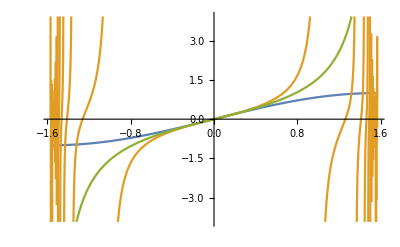

```mathematica
Plot[{Sin[x],Tan[Tan[x]],Tan[x]},{x,-Pi/2,Pi/2}]
```

```mathematica
D[ArcCos[x],x]/.x->Sin[t]
```

-1/(√(1-Sin[t]^2))

```mathematica
Sec[Pi/4]
```

√2

```mathematica
ArcCos[Sin[t]/Sqrt[2]]//FullSimplify
```

ArcCos[Sin[t]/(√2)]

```mathematica
FullSimplify[2(ArcCos[Sin[t]/Sqrt[2]]+t-Pi/2)]
```

2 (t-ArcSin[Sin[t]/(√2)])

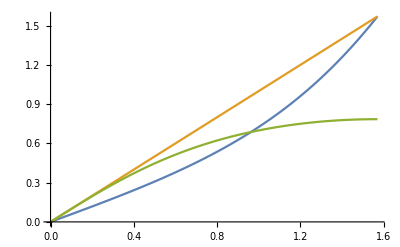

```mathematica
Plot[{2(-ArcSin[Sin[t]/Sqrt[2]]+t),t,ArcTan[Sin[t]]},{t,0,Pi/2}]
```

```mathematica
Limit[(ArcCos[Sin[t]/n]+t-Pi/2),t->Pi/2]
```

ArcCos[1/n]

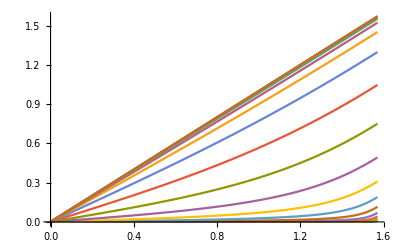

```mathematica
Plot[Evaluate@Table[(ArcCos[Sin[t]/n]+t-Pi/2),{n,1+Exp[Range[-10,10,1]]}],{t,0,Pi/2}]
```

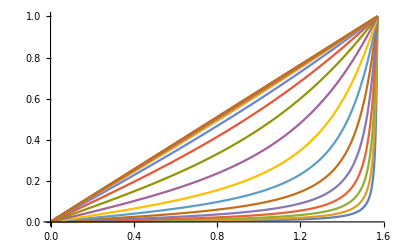

```mathematica
Plot[Evaluate@Table[(ArcCos[Sin[t]/n]+t-Pi/2)/ArcCos[1/n],{n,1+Exp[Range[-10,10,1]]}],{t,0,Pi/2}]
```

```mathematica
D[(ArcCos[Sin[t]/n]+t-Pi/2),t]//FullSimplify
```

1-Cos[t]/(n √(1-Sin[t]^2/n^2))

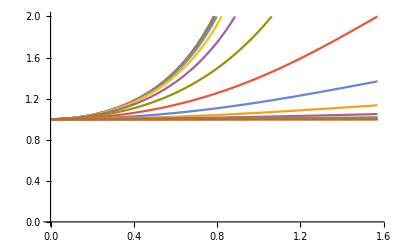

```mathematica
Plot[Evaluate@Table[(1-Cos[t]/(n √(1-Sin[t]^2/n^2)))/(1-1/n),{n,1+Exp[Range[-10,10,1]]}],{t,0,Pi/2},PlotRange->{0,2}]
```

```mathematica
Limit[(1-Cos[t]/(n √(1-Sin[t]^2/n^2))),t->Pi/2]
```

1

```mathematica
Limit[(1-Cos[t]/(n √(1-Sin[t]^2/n^2)))/(1-1/n)/.t->1,n->1]
```

Sec[1]^2

```mathematica
N[%]
```

3.42552

```mathematica
Integrate[Sec[x]^2,x]
```

Tan[x]

```mathematica
Limit[(t-ArcSin[Sin[t]/n])/(t(1-1/n)),n->1]
```

DirectedInfinity[t-ArcSin[Sin[t]]]/t

```mathematica
?DirectedInfinity
```

DirectedInfinity[] represents an infinite numerical quantity whose direction in the complex plane is unknown. 
DirectedInfinity[z] represents an infinite numerical quantity that is a positive real multiple of the complex number z.

```mathematica
Tan[2(ArcCos[Sin[Pi/2]/1.33]+Pi/2-Pi/2)]
```

7.58866

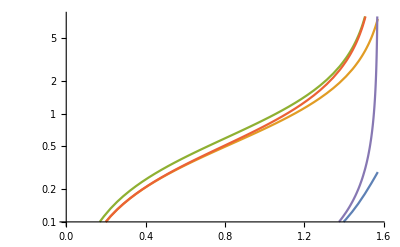

```mathematica
LogPlot[Evaluate@Join[Table[Tan[2(ArcCos[Sin[t]/n]+t-Pi/2)],{n,{1.01,1.33,Sqrt[2]}}],{2Tan[t]*(1-1/1.33),2Tan[t]*(1-1/1.01)}],{t,0,Pi/2},PlotRange->{.1,8}]
```

```mathematica
2ArcSec[1.33]/Degree
```

82.4931

```mathematica
Tan[82.49306673734554Degree]
```

7.58866

```mathematica
1/Degree//N
```

57.2958

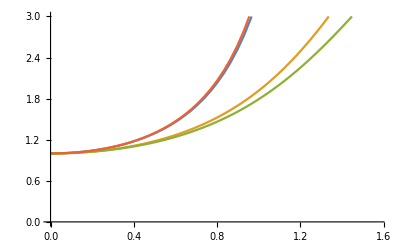

```mathematica
Plot[Evaluate@Join[Table[(1-Cos[t]/(n √(1-Sin[t]^2/n^2)))/(1-1/n),{n,{1.01,1.33,Sqrt[2]}}],{Sec[t]^2}],{t,0,Pi/2},PlotRange->{0,3}]
```

```mathematica
1-1/1.33
```

0.24812

```mathematica
Tan[%]
```

0.274551